# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-8);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/results

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

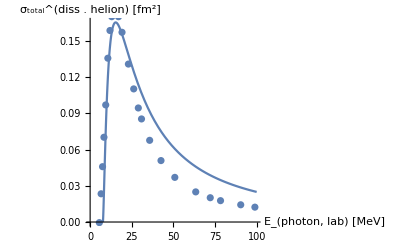

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
MinMax[Eigenvalues[He3Norm]]
```

{6.3956×10^-9,29.7833}

Bad! so He3 eigenvalue will be spurious--or at least run the risk.

```mathematica
dg=Table[He3Norm[[i,i]],{i,1,Length[He3Norm]}];Take[dg,4]
SymmetricMatrixQ[He3Norm]
```

{1.,1.,1.,1.}

True

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {6.3956×10^-9,29.7833}

(min/max) discarded elements: 1 {6.3956×10^-9,6.3956×10^-9}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -7.34416

Dim_full^helion = 96=^!96   ;     Dim_(non - singular)^helion = 95

Norm=1.

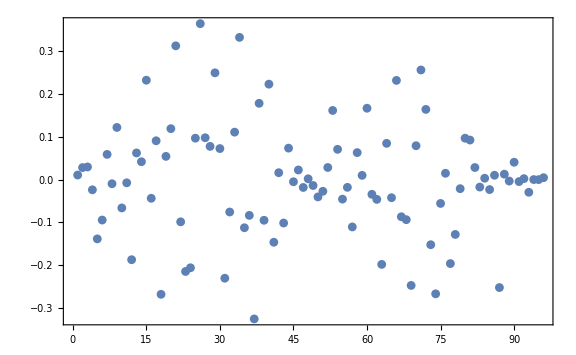
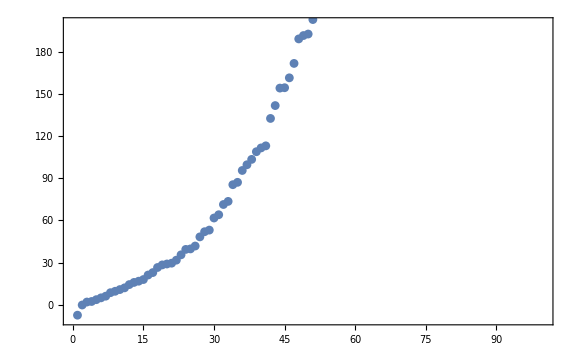
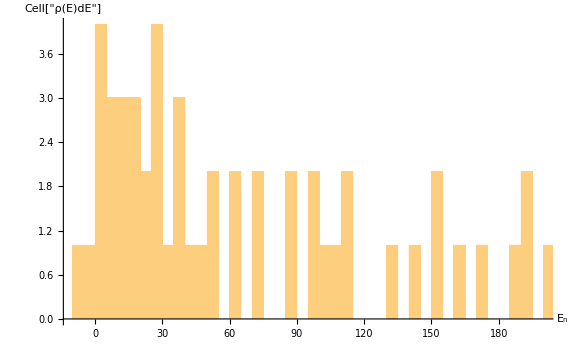
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
MinMax[Eigenvalues[LitNorm[[1]]]]
```

N_final = {210}

{7.27732×10^-8,26.3507}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

Final-state Basis dimension = {210}

min/max: {7.27732×10^-8,26.3507}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.58887,-0.361138,0.12401,0.1702,0.190476}

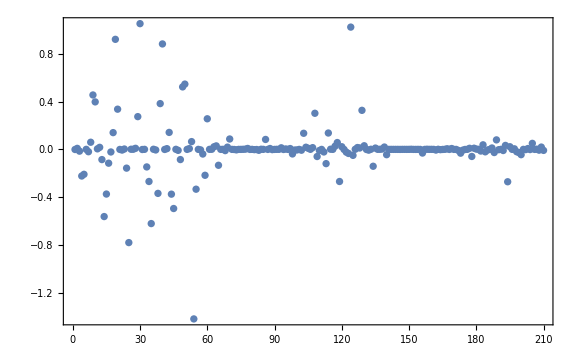
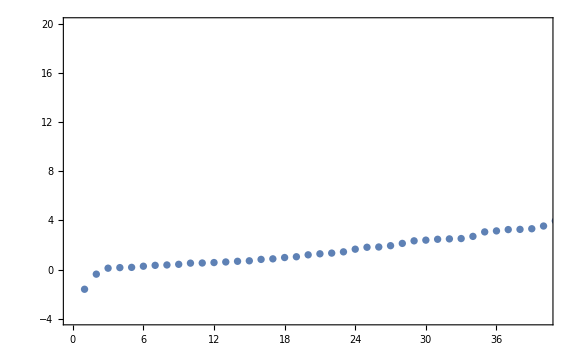
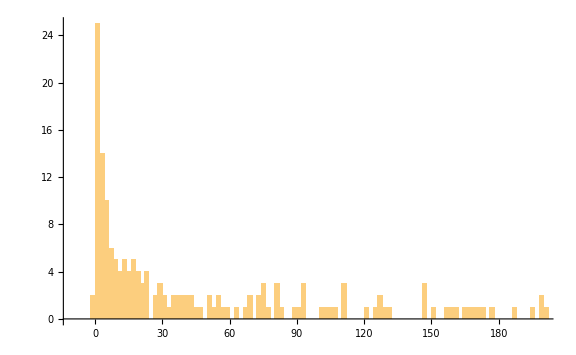
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
dE=2.;
Do[
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[1]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];
Print[Grid[{{
ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,40},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]],{nj,Range[1,Length[Subscript[I, n]]]}];
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt;
tmp =BinaryReadList[fntmp,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
Print[Dimensions[tmp][[1]]];
test=ArrayReshape[tmp,{OutDim,He3BasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

20160

20160

Dim(⟨ψ|ο̂|helion⟩) = {1,210,96}

Dim(⟨ψ|Ĥ|ψ⟩) = {1,210,210}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1,210,210}

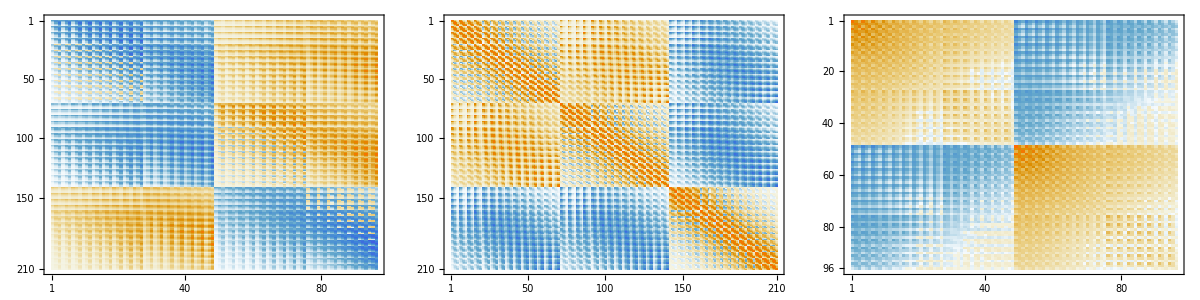

```mathematica
Grid[{{
MatrixPlot[Chop[CouplingBlockj[[1]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[LitNorm[[1]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Medium,PlotRange->Full]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Medium,PlotRange->Full]
}}]
```

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-7.34416 norm=1.

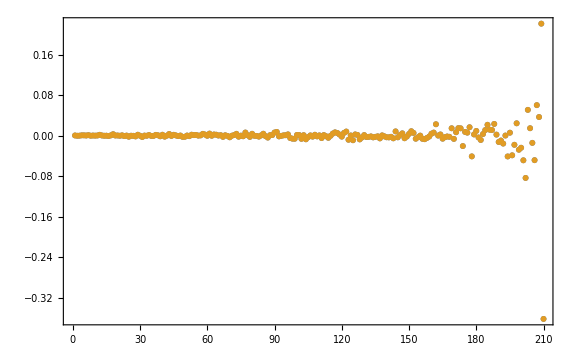

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB;tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];Print[ListPlot[inhomoEB[[1]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]]
,{nj,Range[1,Length[Subscript[I, n]]]}
];
```

That looks rather dodgy! Is the normalisation consistent?

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-7.34416

{1.,-7.34416}

E_0^initial = -7.34416    dim(initial) = {95}

E_0^final  = -1.58887    dim(final)   = {210}

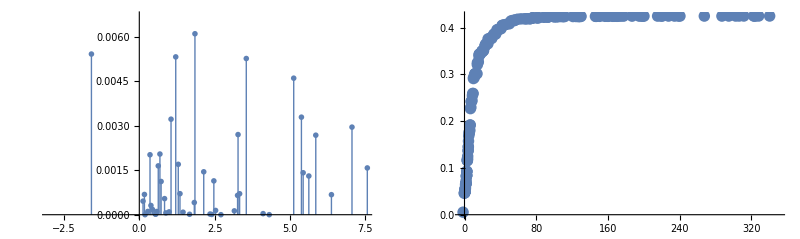

```mathematica
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockj[[nj]][[mm]][[2]].EvecGSiEV);
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];
CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];
Print[GraphicsRow[{
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
,
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
},ImageSize->Full]]

,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

```mathematica
ListPlot[CumStrengthsEV->Range[Length[EvalsFEV]],Joined->False,ImageSize->ImgSize,PlotRange->{{-2.3,10.},{0,0.17}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotStyle->PointSize[0.01]]
```

-Graphics-

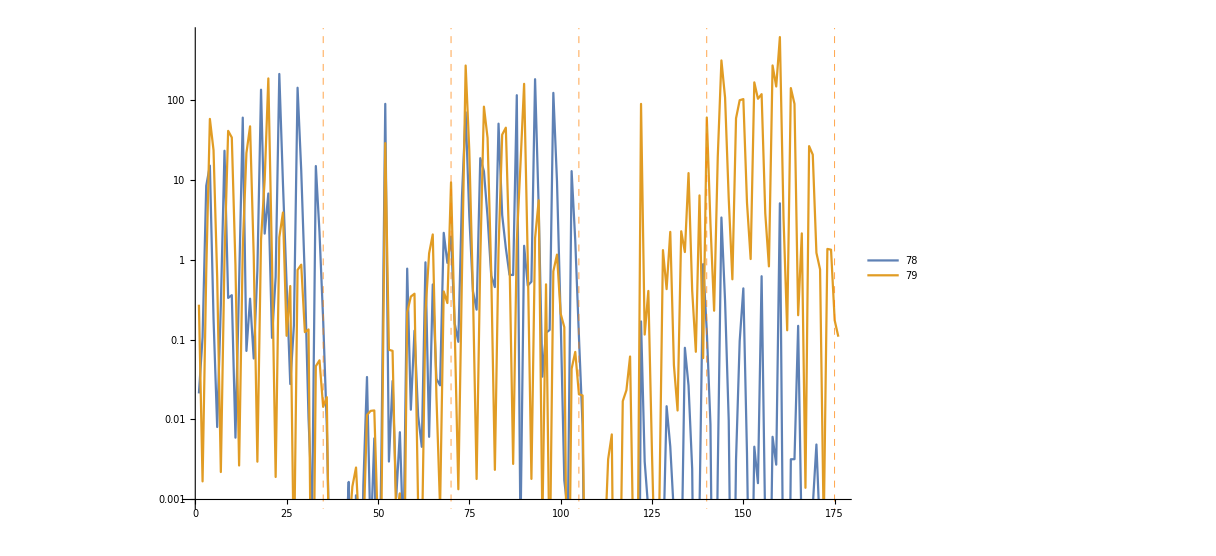
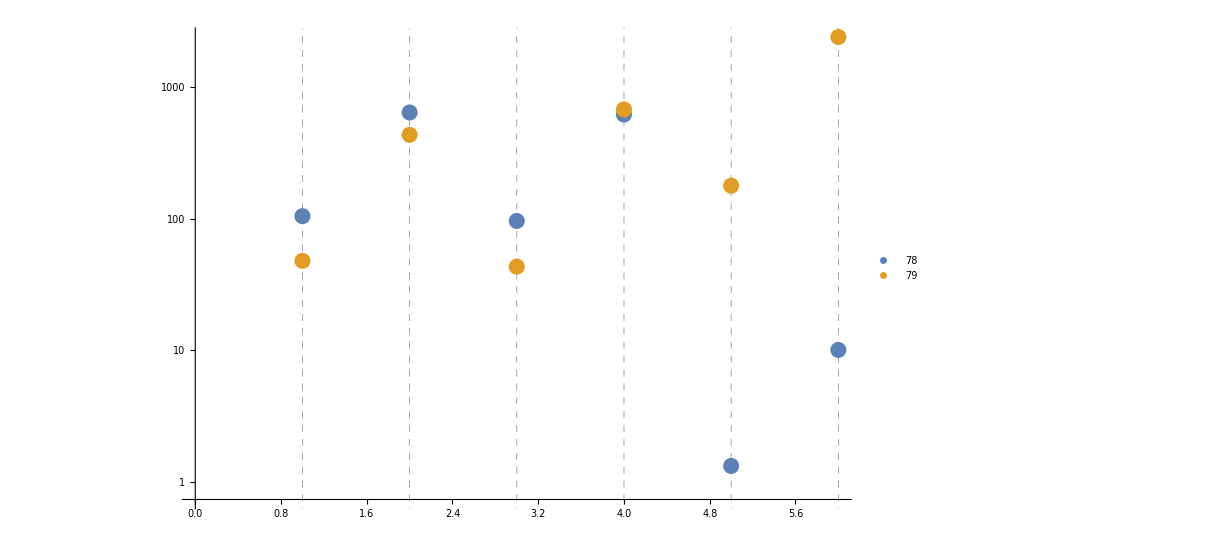
-Graphics- | -Graphics-

```mathematica
InitialStateFrags=Flatten[Import[resultsDir<>"/../basis_struct/LITbas_dims_J0.5_npp0.5^+.dat","Table"]];
FinalStateFrags=Flatten[Import[resultsDir<>"/../basis_struct/LITbas_dims_J0.5_0.5^-.dat","Table"]];
zerlPERfrag=1;
Length[FinalStateFrags];
Total[FinalStateFrags];
ArrayReshape[FinalStateFrags,{Length[FinalStateFrags]/zerlPERfrag,zerlPERfrag}];
gl={Accumulate[FinalStateFrags],None};
f1=1;
f2=Min[12,Length[FinalStateFrags]];
BVrange=Range[Accumulate[FinalStateFrags][[f1]],Accumulate[FinalStateFrags][[f2]]];
selectionInices={78,79};(*{14,15};*)
selectionEVs=Sort[Transpose[{EvalsFEV,EvecsFEV}],#1[[1]]<#2[[1]]&][[selectionInices]][[All,2]];
selectionEVs2=(OμLHSEV.#)^2&/@selectionEVs;
fragRange=Table[Range[Prepend[gl[[1]],1][[n]],Prepend[gl[[1]],1][[n+1]]],{n,1,Length[gl[[1]]]}];
frgStr=Table[Total[selectionEVs2[[nn]][[#]]]&/@fragRange,{nn,Length[selectionInices]}];
Grid[{{
ListLogPlot[selectionEVs2[[All,BVrange]],Joined->True,GridLines->gl,GridLinesStyle->Directive[Orange,Dashed,Thick],PlotLegends->selectionInices,ImageSize->ImgSize,PlotRange->{All,{0.001,Automatic}}],
ListLogPlot[frgStr,Joined->False,GridLines->{Range[Length[gl[[1]]]],None},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotLegends->selectionInices,ImageSize->ImgSize]
}}]
```